```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=28;
Ly=28;
A=Lx*Ly;
```

```mathematica
B=1;
```

```mathematica
(*--- We choose gauge A = (-By,0,0) ---*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2 Exp[I B k],sx2d[j+1+k Lx,j+k Lx]=I/2 Exp[-I B k]},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2 Exp[I B k],sx2dp[1+k Lx,(k+1)Lx]=I/2 Exp[-I B k]},{k,0,Ly-1}]

SX2DP=Table[sx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2 Exp[I B k],cx2d[j+1+k Lx,j+k Lx]=1/2 Exp[-I B k]},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2 Exp[I B k],cx2dp[1+k Lx,(1+k)Lx]=1/2 Exp[-I B k]},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHI]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianQAHI[t_,t0_,m_,αx_, αy_]:=t*(KroneckerProduct[SX2D+αx*SX2DP,σ1]+KroneckerProduct[SY2D+αy*SY2DP, σ2])+KroneckerProduct[-m*Cons+t0*(CX2D+CY2D+αx*CX2DP+αy*CY2DP),σ3]
```

```mathematica
HamiltonianQAHI2[t_,t0_,m_,αx_, αy_]:=t*(KroneckerProduct[SX2D+αx*SX2DP,σ1]+KroneckerProduct[SY2D+αy*SY2DP, σ2])
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Max[Abs[ConjugateTranspose[HamiltonianQAHI[1.0,1.0,1.5,0.0]] - HamiltonianQAHI[1.0,1.0,1.5,0.0]//Chop]]
```

Abs[ConjugateTranspose[HamiltonianQAHI[1.,1.,1.5,0]]-HamiltonianQAHI[1.,1.,1.5,0]]

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
{val,vec}=Eigensystem[HamiltonianQAHI2[1.0,1.0,1,0.0,0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

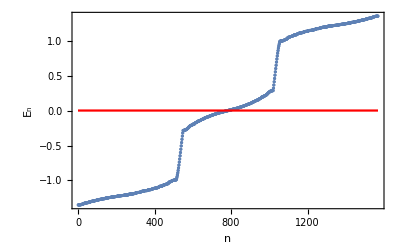

```mathematica
Show[ListPlot[ValAHI,Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}}],Plot[0,{x,0,2A},PlotStyle-> Red],BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

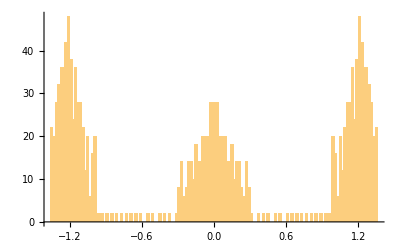

```mathematica
Histogram[val,100]
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(**----Clear memory for quasicrystal----**)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------------quasicrystal--------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

1568

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+10
LineDn[x_]:=((1+√5)/2)^-1*(x-2)-4
```

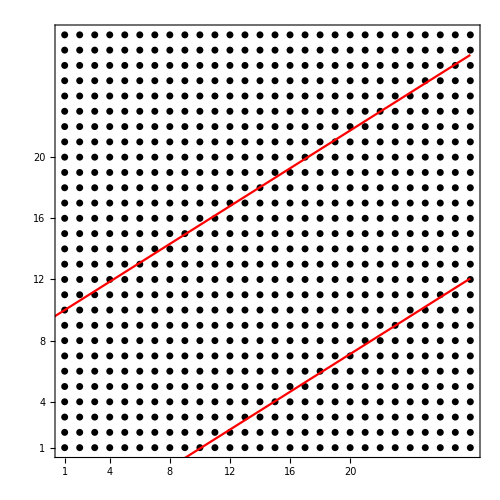

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron, Ux, Vy, P,U,V,LogEigenValuesBott,Bott, BottIndexQuasi]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist=Sort[FibonupNew]
```

{1,2,3,4,5,6,7,8,9,10,29,30,31,32,33,34,35,36,37,38,39,57,58,59,60,61,62,63,64,65,66,67,68,69,85,86,87,88,89,90,91,92,93,94,95,96,97,98,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,520,521,522,523,524,525,526,527,528,529,530,531,532,550,551,552,553,554,555,556,557,558,559,560,579,580,581,582,583,584,585,586,587,588,609,610,611,612,613,614,615,616,639,640,641,642,643,644,668,669,670,671,672,698,699,700,727,728}

```mathematica
(** Fibonup2={}; **)
```

```mathematica
(** Do[Do[Fibonup2=Append[Fibonup2,x+(y-1)*Lx],{y,6,15}],{x,6,15}]**)
```

```mathematica
(** Fibonup2**)
```

```mathematica
(** Clear[Fibonup]**)
```

```mathematica
(** Fibonup = Fibonup2**)
```

```mathematica
YList = Ceiling[Fibonlist/Lx];
```

```mathematica
XList = Fibonlist - (YList - 1)Lx;
```

```mathematica
(**Check that the list is correct**)
```

```mathematica
XList + (YList-1)*Lx - Fibonlist
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
Ux =DiagonalMatrix[ Exp[2 π I XListKron /Lx]];
```

```mathematica
Vy = DiagonalMatrix[Exp[2 π I YListKron/Ly]];
```

```mathematica
(**--Compare with the previous (manually calculated) Fibonup for 20x20 sites--**)
```

```mathematica
(**--Fibonup={1,22,23,43,44,45,65,66,86,87,88,108,109,110,130,131,151,152,153,173,174,194,195,196,216,217,218,238,239,259,260};--**)
```

```mathematica
(**----Group the orbitals in the sites in Fibonlist ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
(**-- Fibondown=Table[Fibonlist[[j]]+A,{j,1,Dimensions[Fibonlist][[1]]}]; --**)
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon = Sort[TotalFibon]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1277,1278,1279,1280,1281,1282,1283,1284,1285,1286,1287,1288,1335,1336,1337,1338,1339,1340,1341,1342,1343,1344,1395,1396,1397,1398,1399,1400,1453,1454,1455,1456}

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

770

```mathematica
NOrbitalsQuasi/2
```

385

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

798

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{1568}

```mathematica
(**-- a=F1;
Do[
a=Drop[a,{TotalFibon[[NOrbitalsQuasi-i]]}],
{i,0,NOrbitalsQuasi-1,1}
] --**)
```

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
HTrial=HamiltonianQAHI[1.,1.,1,1.0,0];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
Hfbfb[i_Integer,j_Integer]=0;
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
]
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
H2d2d[i_Integer,j_Integer]=0;
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
]
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}];
```

```mathematica
(*------------------------------------------------------*)
```

```mathematica
H2dfb[i_Integer,j_Integer]=0;

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
]
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*-------------------------------------------------*)
```

```mathematica
Hfb2d[i_Integer,j_Integer]=0;

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
]
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}];
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon,OnlyEigenvalue]
```

```mathematica
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB);
```

```mathematica
(**------Check that HFibonRenor is Hermitian------**)
```

```mathematica
(** ConjugateTranspose[HFibonRenor] - HFibonRenor//Chop **)
```

```mathematica
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor];
```

```mathematica
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First];
```

```mathematica
ValFibon=Table[{j,ValVecFibon[[j,1]]},{j,1,NOrbitalsQuasi}]//Chop;
```

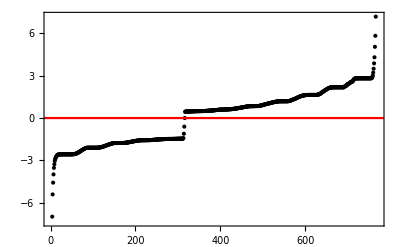

```mathematica
Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black(**,PlotRange->{{0,84},{-2,2}}**)],Plot[0,{x,-100,2A},PlotStyle-> Red]]
```

```mathematica
ValueFibon;
```

```mathematica
ValueFibon = Sort[Re[ValueFibon]];
```

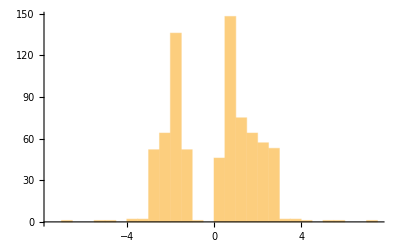

```mathematica
Show[Histogram[Re[ValueFibon]]]
```

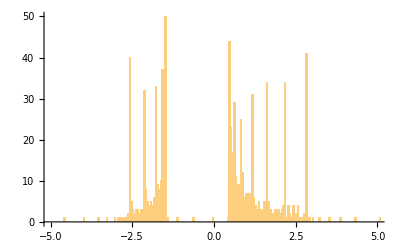

```mathematica
Histogram[Re[ValueFibon]//Chop,5000,PlotRange->{{-5,5},Automatic}]
```

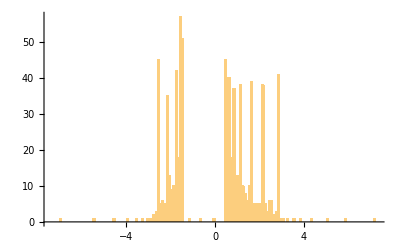

```mathematica
Histogram[Re[ValueFibon]//Chop,3000]
```

```mathematica
OnlyEigenvalue=Table[ValFibon[[j,2]],{j,1,NOrbitalsQuasi}];
```

```mathematica
Tr[OnlyEigenvalue]//Chop
```

252.561

```mathematica
(**---- Calculation of Bott Index of the quasicrystal ----**)
```

```mathematica
FilledEigenvectors=Table[ValVecFibon[[i]][[2]], {i,1,NOrbitalsQuasi/2}];
```

```mathematica
(** We create a projector P on the space of filled eigenstates **)
```

```mathematica
P = Table[0,{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}];
```

```mathematica
Do[P+=TensorProduct[FilledEigenvectors[[i]] ,Conjugate[ FilledEigenvectors[[i]]]],{i, 1, NOrbitalsQuasi/2}];
```

```mathematica
Dimensions[P]
```

{770,770}

```mathematica
U = P . Ux . P + IdentityMatrix[NOrbitalsQuasi] - P;
```

```mathematica
V = P . Vy . P + IdentityMatrix[NOrbitalsQuasi] - P;
```

```mathematica
(** To save computer from hanging, we clear some memory **)
```

```mathematica
Clear[ Bott, LogEigenValuesBott, BottIndexQuasi]
```

```mathematica
Bott = U.V.ConjugateTranspose[U].ConjugateTranspose[V];
```

```mathematica
Clear[P,U,V, Ux, Vy]
```

```mathematica
LogEigenValuesBott=Log[Eigenvalues[Bott]];
```

Bott index of quasicrystal

```mathematica
BottIndexQuasi = Re[(I/(2π))Total[LogEigenValuesBott]]
```

-4.24074×10^-15

```mathematica
percentageOfOrbitalsInside = N[NOrbitalsQuasi/(2*A)]
```

0.491071

```mathematica
NSitesInside = NOrbitalsQuasi/2
```

385

```mathematica
(*---------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*---------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[τ,ν,x,Fibon1D,largestX]
```

```mathematica
τ=1/D[LineUp[x],x];
ν=√(1+τ^2);
```

```mathematica
x[m_]:=m/ν+1/(τ*ν)*Round[m/τ]
```

```mathematica
Fibon1D=Table[{1+N[x[m]],0},{m,0,NOrbitalsQuasi/2}];
Dimensions[Fibon1D]
```

{386,2}

```mathematica
largestX=Ceiling[Fibon1D[[Dimensions[Fibon1D][[1]],1]]]
```

281

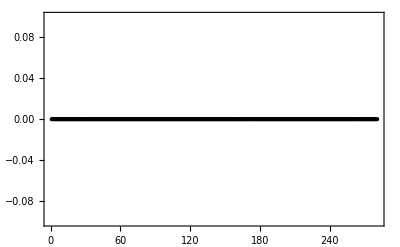

```mathematica
ListPlot[Fibon1D,Frame-> True,Axes-> False,PlotRange->{{0,largestX},{-0.1,0.1}},PlotStyle-> Black]
```

```mathematica
Fibon1D[[3,1]]
```

2.37638

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
ValFibon[[(NOrbitalsQuasi/2)+1,2]]
```

0.554394

```mathematica
Clear[J,TabDataFibon,TDFibon,TabFibonacci]
```

```mathematica
J=NOrbitalsQuasi/2;
```

```mathematica
TabDataFibon=Table[{Fibon1D[[i,1]],0,
Abs[ValVecFibon[[J,2,i]]]^2+Abs[ValVecFibon[[J,2,i+NOrbitalsQuasi/2]]]^2

+Abs[ValVecFibon[[J+1,2,i]]]^2+Abs[ValVecFibon[[J+1,2,i+NOrbitalsQuasi/2]]]^2

},{i,1,NOrbitalsQuasi/2}];
```

```mathematica
TDFibon=Flatten[TabDataFibon];
```

```mathematica
TabFibonacci=Table[{TDFibon[[i]],TDFibon[[i+1]],TDFibon[[i+2]]},{i,1,3*NOrbitalsQuasi/2,3}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[colorfunc,rng,P1]
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
rng={0,Max[#]}&@TabFibonacci[[All,3]];
```

```mathematica
rng[[2]]
```

0.0184117

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 12},Ticks-> {{0,"0.00"},{rng[[2]]/2,"0.05"},{rng[[2]]-10^-3,"0.10"}}]
```

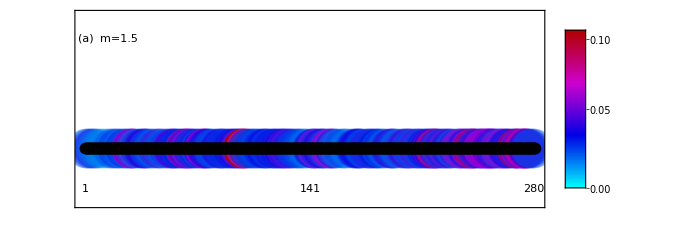

```mathematica
Show[Graphics[{PointSize[0.05],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibonacci,
Frame->True,FrameTicks-> {None,None},FrameStyle-> Black,
BaseStyle-> 18,
PlotRange-> {{0.0,largestX},{-3.5,8.5}}],
ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.015]}]
,
Epilog-> {Inset[1,{1,-2.5}],Inset[Ceiling[largestX/2],{Ceiling[largestX/2],-2.5}],Inset[largestX-1,{largestX-1,-2.5}],
Rotate[Inset[P1,{10.5,5.00}],90 Degree],Inset["m=1.5",{21.5,7}],
Inset["(a)",{1.25,7}]
}
]
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
ArrayPlot[Re[HFBFB[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
ArrayPlot[Im[HFBFB[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
ArrayPlot[Re[HFibonRenor[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
ArrayPlot[Im[HFibonRenor[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```

-Graphics-